```mathematica
NSolve[Erf[x]-(-1)==0.000001,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-3.45891}}

```mathematica
f[x_,c_,e_]:=Exp[-(x-c)^2/(2*e)];
h[x_,b_,e_]:=0.5*(Erf[100*Abs[x-b]^1-2.75106]+1);
k[x_,c_,e_,b_]:=-Exp[-(x-c-b)^2/(0.002*e)]+1
```

General::munfl: Exp[-3003.4] is too small to represent as a normalized machine number; precision may be lost.

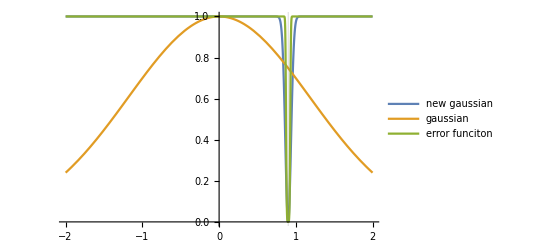

```mathematica
c=0; e=1.4;b1=0.9; b2=3;
Plot[{k[x,c,e,b1],f[x,c,e],h[x,b1,e]},{x,c-2,2},GridLines->{{b1,b2},{}},
PlotLegends->{"new gaussian","gaussian", "error funciton"},PlotRange->Full]
```

```mathematica
N[Exp[-1/(2*0.5)]]
```

0.367879